```mathematica
dataPureBFSyy={498138,101129,47404,46614,24887,24492,43849,61230,21332,20937,1001807,131942,117721,156434,68736,95203,64391,80587,107449,135892,1785556,645881,543963,354741,466140,250056,276919,244921,352371,371333,5249612,2527430,2453954,1232507,369358,381999,341310,346445,835102,502879,16380102,4996790,2019021,1065013,1095035,1042891,1199325,1812813,1117948,1002203,50449451,10635117,12848494,15177223,13311475,13310290,15151545,13209556,11393187,14713057,211902387,152960486,177132247,200924380,167399785,150194455,164553167,155088932,178416110,167318802,2634719180,2285672695,2396775729,2543122155,2280792044,2434949090,2442000455,2323558075,2207597697,2338486821,39508600886,39901100764,40383445292,39151426963,41663136771,38433490623,41936982135,36233867881,39895316670,39492600413}
```

{498138,101129,47404,46614,24887,24492,43849,61230,21332,20937,1001807,131942,117721,156434,68736,95203,64391,80587,107449,135892,1785556,645881,543963,354741,466140,250056,276919,244921,352371,371333,5249612,2527430,2453954,1232507,369358,381999,341310,346445,835102,502879,16380102,4996790,2019021,1065013,1095035,1042891,1199325,1812813,1117948,1002203,50449451,10635117,12848494,15177223,13311475,13310290,15151545,13209556,11393187,14713057,211902387,152960486,177132247,200924380,167399785,150194455,164553167,155088932,178416110,167318802,2634719180,2285672695,2396775729,2543122155,2280792044,2434949090,2442000455,2323558075,2207597697,2338486821,39508600886,39901100764,40383445292,39151426963,41663136771,38433490623,41936982135,36233867881,39895316670,39492600413}

```mathematica
Table[2^i,{i,2,4},{j,1,10}]
```

{{4,4,4,4,4,4,4,4,4,4},{8,8,8,8,8,8,8,8,8,8},{16,16,16,16,16,16,16,16,16,16}}

```mathematica
dataPureBFSxx={4,4,4,4,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,16,16,16,16,16,16,16,16,16,16,32,32,32,32,32,32,32,32,32,32,64,64,64,64,64,64,64,64,64,64,128,128,128,128,128,128,128,128,128,128,256,256,256,256,256,256,256,256,256,256,512,512,512,512,512,512,512,512,512,512,1024,1024,1024,1024,1024,1024,1024,1024,1024,1024}
```

{4,4,4,4,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,16,16,16,16,16,16,16,16,16,16,32,32,32,32,32,32,32,32,32,32,64,64,64,64,64,64,64,64,64,64,128,128,128,128,128,128,128,128,128,128,256,256,256,256,256,256,256,256,256,256,512,512,512,512,512,512,512,512,512,512,1024,1024,1024,1024,1024,1024,1024,1024,1024,1024}

```mathematica
datapureBFS=Transpose@{dataPureBFSxx,dataPureBFSyy}
```

{{4,498138},{4,101129},{4,47404},{4,46614},{4,24887},{4,24492},{4,43849},{4,61230},{4,21332},{4,20937},{8,1001807},{8,131942},{8,117721},{8,156434},{8,68736},{8,95203},{8,64391},{8,80587},{8,107449},{8,135892},{16,1785556},{16,645881},{16,543963},{16,354741},{16,466140},{16,250056},{16,276919},{16,244921},{16,352371},{16,371333},{32,5249612},{32,2527430},{32,2453954},{32,1232507},{32,369358},{32,381999},{32,341310},{32,346445},{32,835102},{32,502879},{64,16380102},{64,4996790},{64,2019021},{64,1065013},{64,1095035},{64,1042891},{64,1199325},{64,1812813},{64,1117948},{64,1002203},{128,50449451},{128,10635117},{128,12848494},{128,15177223},{128,13311475},{128,13310290},{128,15151545},{128,13209556},{128,11393187},{128,14713057},{256,211902387},{256,152960486},{256,177132247},{256,200924380},{256,167399785},{256,150194455},{256,164553167},{256,155088932},{256,178416110},{256,167318802},{512,2634719180},{512,2285672695},{512,2396775729},{512,2543122155},{512,2280792044},{512,2434949090},{512,2442000455},{512,2323558075},{512,2207597697},{512,2338486821},{1024,39508600886},{1024,39901100764},{1024,40383445292},{1024,39151426963},{1024,41663136771},{1024,38433490623},{1024,41936982135},{1024,36233867881},{1024,39895316670},{1024,39492600413}}

```mathematica
Clear[datapureBFS]
```

```mathematica
model[v_] = Fit[datapureBFS,{v^2},v]
```

36002.6 v^2

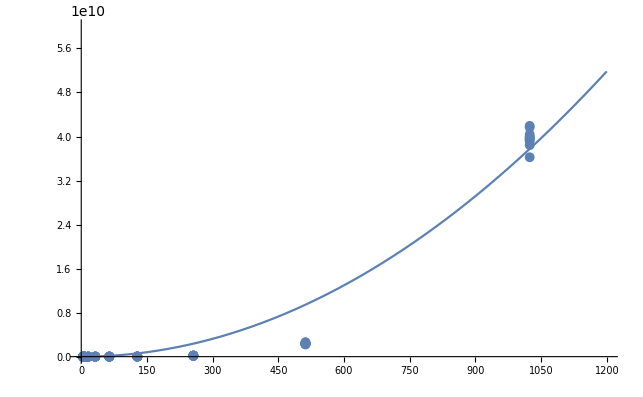

```mathematica
Show[ListPlot[datapureBFS,PlotRange->{{0,1200},{0,6*10^10}}],Plot[model[v],{v,0,1200}]]
```

```mathematica
dataPureDijyy={540803,86118,45034,33578,45824,23307,20542,21727,27653,19752,819301,137472,95598,76637,71107,88882,97969,54515,56884,90068,1273196,310497,329458,368172,310102,336174,321558,331039,356716,127596,3802207,2293175,2320037,1563547,395825,454685,379628,493793,496954,686965,13478180,4818234,3116821,619019,675509,695260,786119,636005,673929,592552,30525889,3240072,3863832,3889508,3376754,3463662,3054011,3193458,2197181,1843230,42103954,18672091,14365427,13313450,12871802,14978125,15640597,17451040,12880493,14824062,184264989,163151980,190233564,177188343,118396160,152584019,160536852,143978984,188096033,141488688,1782492074,1604431101,1723792726,1603504745,1551822787,1586039484,1608260565,1588239825,1565340865,1593274144}
```

{540803,86118,45034,33578,45824,23307,20542,21727,27653,19752,819301,137472,95598,76637,71107,88882,97969,54515,56884,90068,1273196,310497,329458,368172,310102,336174,321558,331039,356716,127596,3802207,2293175,2320037,1563547,395825,454685,379628,493793,496954,686965,13478180,4818234,3116821,619019,675509,695260,786119,636005,673929,592552,30525889,3240072,3863832,3889508,3376754,3463662,3054011,3193458,2197181,1843230,42103954,18672091,14365427,13313450,12871802,14978125,15640597,17451040,12880493,14824062,184264989,163151980,190233564,177188343,118396160,152584019,160536852,143978984,188096033,141488688,1782492074,1604431101,1723792726,1603504745,1551822787,1586039484,1608260565,1588239825,1565340865,1593274144}

```mathematica
dataPureDijxx=dataPureBFSxx
```

{4,4,4,4,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,16,16,16,16,16,16,16,16,16,16,32,32,32,32,32,32,32,32,32,32,64,64,64,64,64,64,64,64,64,64,128,128,128,128,128,128,128,128,128,128,256,256,256,256,256,256,256,256,256,256,512,512,512,512,512,512,512,512,512,512,1024,1024,1024,1024,1024,1024,1024,1024,1024,1024}

```mathematica
datapureDij=Transpose@{dataPureDijxx,dataPureDijyy}
```

{{4,540803},{4,86118},{4,45034},{4,33578},{4,45824},{4,23307},{4,20542},{4,21727},{4,27653},{4,19752},{8,819301},{8,137472},{8,95598},{8,76637},{8,71107},{8,88882},{8,97969},{8,54515},{8,56884},{8,90068},{16,1273196},{16,310497},{16,329458},{16,368172},{16,310102},{16,336174},{16,321558},{16,331039},{16,356716},{16,127596},{32,3802207},{32,2293175},{32,2320037},{32,1563547},{32,395825},{32,454685},{32,379628},{32,493793},{32,496954},{32,686965},{64,13478180},{64,4818234},{64,3116821},{64,619019},{64,675509},{64,695260},{64,786119},{64,636005},{64,673929},{64,592552},{128,30525889},{128,3240072},{128,3863832},{128,3889508},{128,3376754},{128,3463662},{128,3054011},{128,3193458},{128,2197181},{128,1843230},{256,42103954},{256,18672091},{256,14365427},{256,13313450},{256,12871802},{256,14978125},{256,15640597},{256,17451040},{256,12880493},{256,14824062},{512,184264989},{512,163151980},{512,190233564},{512,177188343},{512,118396160},{512,152584019},{512,160536852},{512,143978984},{512,188096033},{512,141488688},{1024,1782492074},{1024,1604431101},{1024,1723792726},{1024,1603504745},{1024,1551822787},{1024,1586039484},{1024,1608260565},{1024,1588239825},{1024,1565340865},{1024,1593274144}}

```mathematica
model2[v_] = Fit[datapureDij,v^2,v]
```

1486.33 v^2

```mathematica
model22[v_]=Normal[model2[v]]
```

-9.83132×10^7+210992. v Log[v]

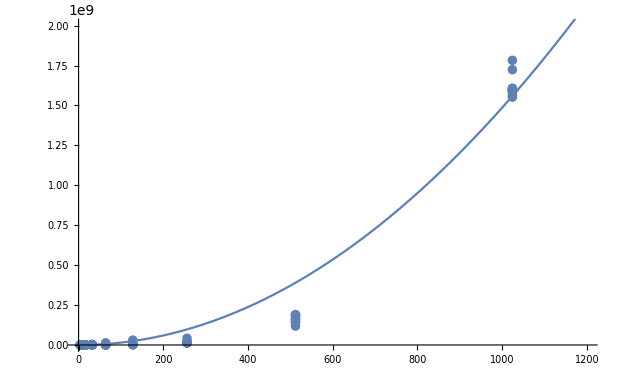

```mathematica
Show[ListPlot[datapureDij,PlotRange->{{0,1200},{0,2*10^9}}],Plot[model2[v],{v,0,1200}]]
```

```mathematica
1593274144
```

1593274144

```mathematica
ScientificForm[N[1593274144,10]]
```

1.593274144×10^9

```mathematica
dataIncreasingDijyy={497743,62021,80192,36738,88882,22912,41873,52144,20937,19752,697631,71106,202257,107845,107449,75847,101524,59650,121671,89673,1064618,361061,381209,379629,320373,350001,305757,340520,363431,223985,3420998,2611178,2337023,2271448,2343739,475226,437698,367777,363037,725678,11858144,4931610,1554855,598477,635215,611908,605588,525791,613489,493003,28174644,3411123,3628391,3180028,3285107,2993571,2991596,2960783,1879574,2091312,45212480,25356469,22437560,15714074,15838905,18851833,18058208,21618654,18888966,13236419,177976831,195929566,218763740,131057804,146105455,194959755,166491995,157792942,208712879,161544584,1660296078,1627755514,1601417383,1646149105,1489694144,1597428325,1589599533,1617210069,1668312907,1634688763}
```

{497743,62021,80192,36738,88882,22912,41873,52144,20937,19752,697631,71106,202257,107845,107449,75847,101524,59650,121671,89673,1064618,361061,381209,379629,320373,350001,305757,340520,363431,223985,3420998,2611178,2337023,2271448,2343739,475226,437698,367777,363037,725678,11858144,4931610,1554855,598477,635215,611908,605588,525791,613489,493003,28174644,3411123,3628391,3180028,3285107,2993571,2991596,2960783,1879574,2091312,45212480,25356469,22437560,15714074,15838905,18851833,18058208,21618654,18888966,13236419,177976831,195929566,218763740,131057804,146105455,194959755,166491995,157792942,208712879,161544584,1660296078,1627755514,1601417383,1646149105,1489694144,1597428325,1589599533,1617210069,1668312907,1634688763}

```mathematica
dataIncreasingDijxx=dataPureDijxx
```

{4,4,4,4,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,16,16,16,16,16,16,16,16,16,16,32,32,32,32,32,32,32,32,32,32,64,64,64,64,64,64,64,64,64,64,128,128,128,128,128,128,128,128,128,128,256,256,256,256,256,256,256,256,256,256,512,512,512,512,512,512,512,512,512,512,1024,1024,1024,1024,1024,1024,1024,1024,1024,1024}

```mathematica
dataincreasingDij=Transpose@{dataIncreasingDijxx,dataIncreasingDijyy}
```

{{4,497743},{4,62021},{4,80192},{4,36738},{4,88882},{4,22912},{4,41873},{4,52144},{4,20937},{4,19752},{8,697631},{8,71106},{8,202257},{8,107845},{8,107449},{8,75847},{8,101524},{8,59650},{8,121671},{8,89673},{16,1064618},{16,361061},{16,381209},{16,379629},{16,320373},{16,350001},{16,305757},{16,340520},{16,363431},{16,223985},{32,3420998},{32,2611178},{32,2337023},{32,2271448},{32,2343739},{32,475226},{32,437698},{32,367777},{32,363037},{32,725678},{64,11858144},{64,4931610},{64,1554855},{64,598477},{64,635215},{64,611908},{64,605588},{64,525791},{64,613489},{64,493003},{128,28174644},{128,3411123},{128,3628391},{128,3180028},{128,3285107},{128,2993571},{128,2991596},{128,2960783},{128,1879574},{128,2091312},{256,45212480},{256,25356469},{256,22437560},{256,15714074},{256,15838905},{256,18851833},{256,18058208},{256,21618654},{256,18888966},{256,13236419},{512,177976831},{512,195929566},{512,218763740},{512,131057804},{512,146105455},{512,194959755},{512,166491995},{512,157792942},{512,208712879},{512,161544584},{1024,1660296078},{1024,1627755514},{1024,1601417383},{1024,1646149105},{1024,1489694144},{1024,1597428325},{1024,1589599533},{1024,1617210069},{1024,1668312907},{1024,1634688763}}

```mathematica
model3[v_] = Fit[dataincreasingDij,v^2,v]
```

1482.97 v^2

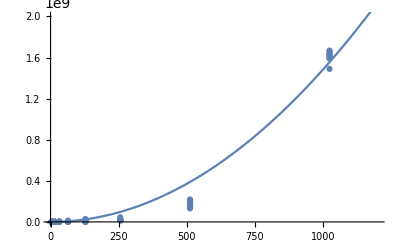

```mathematica
Show[ListPlot[dataincreasingDij,PlotRange->{{0,1200},{0,2*10^9}}],Plot[model3[v],{v,0,1200}]]
```

```mathematica
dataincreasingBFSyy={461795,45824,47009,34763,25282,27652,30022,55305,21727,23307,952823,120880,129177,105869,145768,79007,91253,67156,76636,63600,2083412,397009,340520,407280,412811,346445,331039,243737,383973,306942,5182456,1885894,1874438,1459653,361852,523816,604007,343680,738714,767947,18970343,5178506,1568287,1432395,1476639,1469133,1326131,1030645,843793,1373140,44222918,10145669,9436977,11143921,9488727,12152049,9602497,9975409,7972980,9781052,122824496,109316689,111063136,93711644,89865590,93062603,102606635,104133443,86136860,90428513,1127726083,1084514848,967769537,1078211284,992140396,1022268485,1021742299,1041782001,1063383272,992676457,13702352627,12600627315,15049289630,14076505525,15061360301,14867503086,14662453756,13747698629,13569159663,14314119517}
```

{461795,45824,47009,34763,25282,27652,30022,55305,21727,23307,952823,120880,129177,105869,145768,79007,91253,67156,76636,63600,2083412,397009,340520,407280,412811,346445,331039,243737,383973,306942,5182456,1885894,1874438,1459653,361852,523816,604007,343680,738714,767947,18970343,5178506,1568287,1432395,1476639,1469133,1326131,1030645,843793,1373140,44222918,10145669,9436977,11143921,9488727,12152049,9602497,9975409,7972980,9781052,122824496,109316689,111063136,93711644,89865590,93062603,102606635,104133443,86136860,90428513,1127726083,1084514848,967769537,1078211284,992140396,1022268485,1021742299,1041782001,1063383272,992676457,13702352627,12600627315,15049289630,14076505525,15061360301,14867503086,14662453756,13747698629,13569159663,14314119517}

```mathematica
dataincreasingBFSxx=dataIncreasingDijxx
```

{4,4,4,4,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,16,16,16,16,16,16,16,16,16,16,32,32,32,32,32,32,32,32,32,32,64,64,64,64,64,64,64,64,64,64,128,128,128,128,128,128,128,128,128,128,256,256,256,256,256,256,256,256,256,256,512,512,512,512,512,512,512,512,512,512,1024,1024,1024,1024,1024,1024,1024,1024,1024,1024}

```mathematica
dataincreasingBFS=Transpose@{dataincreasingBFSxx,dataincreasingBFSyy}
```

{{4,461795},{4,45824},{4,47009},{4,34763},{4,25282},{4,27652},{4,30022},{4,55305},{4,21727},{4,23307},{8,952823},{8,120880},{8,129177},{8,105869},{8,145768},{8,79007},{8,91253},{8,67156},{8,76636},{8,63600},{16,2083412},{16,397009},{16,340520},{16,407280},{16,412811},{16,346445},{16,331039},{16,243737},{16,383973},{16,306942},{32,5182456},{32,1885894},{32,1874438},{32,1459653},{32,361852},{32,523816},{32,604007},{32,343680},{32,738714},{32,767947},{64,18970343},{64,5178506},{64,1568287},{64,1432395},{64,1476639},{64,1469133},{64,1326131},{64,1030645},{64,843793},{64,1373140},{128,44222918},{128,10145669},{128,9436977},{128,11143921},{128,9488727},{128,12152049},{128,9602497},{128,9975409},{128,7972980},{128,9781052},{256,122824496},{256,109316689},{256,111063136},{256,93711644},{256,89865590},{256,93062603},{256,102606635},{256,104133443},{256,86136860},{256,90428513},{512,1127726083},{512,1084514848},{512,967769537},{512,1078211284},{512,992140396},{512,1022268485},{512,1021742299},{512,1041782001},{512,1063383272},{512,992676457},{1024,13702352627},{1024,12600627315},{1024,15049289630},{1024,14076505525},{1024,15061360301},{1024,14867503086},{1024,14662453756},{1024,13747698629},{1024,13569159663},{1024,14314119517}}

```mathematica
model4[v_] = Fit[dataincreasingBFS,v^2,v]
```

12902.7 v^2

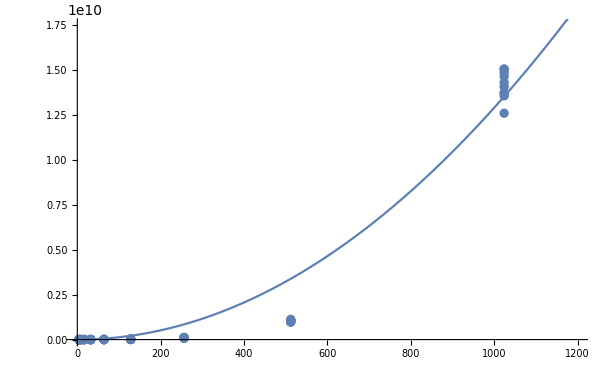

```mathematica
Show[ListPlot[dataincreasingBFS,PlotRange->{{0,1200},{0,1.75*10^10}}],Plot[model4[v],{v,0,1200}]]
```

```mathematica
dataincreasingBruteyy={32449707,352766,224774,269413,135892,120485,123250,120881,100734,120881,8364854,2511234,2687815,3308413,3420208,3934148,3348312,2091708,1408692,1293343,54402710727,49508183335,44729054584,55571460344,52004964002,43769434607,56012156789,54863641230,47182143259,45151013757}
```

{32449707,352766,224774,269413,135892,120485,123250,120881,100734,120881,8364854,2511234,2687815,3308413,3420208,3934148,3348312,2091708,1408692,1293343,54402710727,49508183335,44729054584,55571460344,52004964002,43769434607,56012156789,54863641230,47182143259,45151013757}

```mathematica
dataincreasingBrutexx={4,4,4,4,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,16,16,16,16,16,16,16,16,16,16}
```

{4,4,4,4,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,16,16,16,16,16,16,16,16,16,16}

```mathematica
dataincreasingBrute=Transpose@{dataincreasingBrutexx,dataincreasingBruteyy}
```

{{4,32449707},{4,352766},{4,224774},{4,269413},{4,135892},{4,120485},{4,123250},{4,120881},{4,100734},{4,120881},{8,8364854},{8,2511234},{8,2687815},{8,3308413},{8,3420208},{8,3934148},{8,3348312},{8,2091708},{8,1408692},{8,1293343},{16,54402710727},{16,49508183335},{16,44729054584},{16,55571460344},{16,52004964002},{16,43769434607},{16,56012156789},{16,54863641230},{16,47182143259},{16,45151013757}}

0.00240501 v!

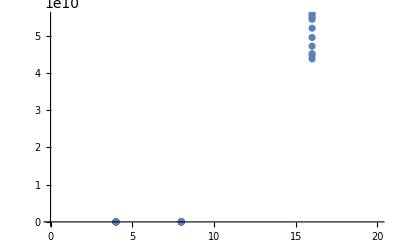

```mathematica
model5[v_] = Fit[dataincreasingBrute,v!,v]
```

```mathematica
Show[ListPlot[dataincreasingBrute,PlotRange->{{0,20},{0,55151013757}}],Plot[model5[v],{v,0,32}]]
```

-Graphics-

```mathematica
100*Abs[61.2721865421079-61.272186279296875]/61.2721865421079
```

4.28924×10^-7

```mathematica
datapureBruteyy={21875426,237811,229515,283239,250846,188431,150113,121671,167494,113375,7571229,2980930,3437984,2895998,10819203,1513377,1272406,1404347,989956,1284256,80335864977,60276242037,64812170615,79421342919,76326746003,62778158942,73196402817,72371204362,60569862035,59178342238}
```

{21875426,237811,229515,283239,250846,188431,150113,121671,167494,113375,7571229,2980930,3437984,2895998,10819203,1513377,1272406,1404347,989956,1284256,80335864977,60276242037,64812170615,79421342919,76326746003,62778158942,73196402817,72371204362,60569862035,59178342238}

```mathematica
datapureBrutexx={4,4,4,4,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,16,16,16,16,16,16,16,16,16,16}
```

{4,4,4,4,4,4,4,4,4,4,8,8,8,8,8,8,8,8,8,8,16,16,16,16,16,16,16,16,16,16}

```mathematica
79421342919./2895998
```

27424.5

```mathematica
datapureBrute=Transpose@{datapureBrutexx,datapureBruteyy}
```

{{4,21875426},{4,237811},{4,229515},{4,283239},{4,250846},{4,188431},{4,150113},{4,121671},{4,167494},{4,113375},{8,7571229},{8,2980930},{8,3437984},{8,2895998},{8,10819203},{8,1513377},{8,1272406},{8,1404347},{8,989956},{8,1284256},{16,80335864977},{16,60276242037},{16,64812170615},{16,79421342919},{16,76326746003},{16,62778158942},{16,73196402817},{16,72371204362},{16,60569862035},{16,59178342238}}

```mathematica
model6[v_] = Fit[datapureBrute,v!,v]
```

0.00329433 v!

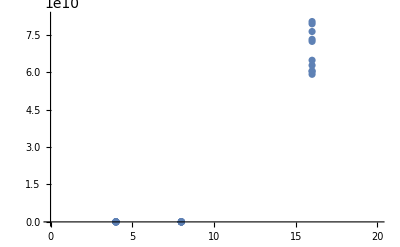

```mathematica
Show[ListPlot[datapureBrute,PlotRange->{{0,20},{0,82371204362}}],Plot[model6[v],{v,0,32}]]
```